```mathematica
SetDirectory["C:\\Users\\ICT_01\\Desktop\\Lab4_2017"]
```

C:\Users\ICT_01\Desktop\Lab4_2017

```mathematica
T1:=Import["image_1.bmp"]
```

```mathematica
T1
```

-Graphics-

```mathematica
ColorSep := ColorSeparate[T1]
```

```mathematica
TG = ColorConvert[T1,"Grayscale"]
```

-Graphics-

```mathematica
Export["image1_gray.bmp",TG]
```

image1_gray.bmp

```mathematica
CRed = ColorSep[[1]]
```

-Graphics-

```mathematica
CGreen = ColorSep[[2]]
```

-Graphics-

```mathematica
CBlue = ColorSep[[3]]
```

-Graphics-

```mathematica
T2 = ColorCombine[{CRed,CGreen,CBlue}]
```

-Graphics-

```mathematica
T3 = ColorCombine[{CGreen,CRed,CBlue}]
```

-Graphics-

```mathematica
M3 = ImageData[CRed];
MatrixForm[M3];
ListPlot3D[M3,ImageSize->Small]
M3Image = Image[M3]
```

-Graphics3D-

-Graphics-

```mathematica
{P1 = Import["baboon.jpg"]}
```

{-Graphics-}

```mathematica
ColorSep2 = ColorSeparate[P1]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{CRed = ColorSep2[[1]]}
```

{-Graphics-}

```mathematica
{CGreen = ColorSep2[[2]]}
```

{-Graphics-}

```mathematica
{CBlue = ColorSep2[[3]]}
```

{-Graphics-}

```mathematica
{P2 = ColorCombine[{CGreen,CRed,CBlue}]}
```

{-Graphics-}

```mathematica
Export["Chi_2.jpg",P2]
```

Chi_2.jpg

```mathematica
{T4 = Import["textold1.jpg"]}
```

{-Graphics-}

```mathematica
Dimensions[ImageData[T4]]
```

{254,332,3}

```mathematica
T4GL=ColorConvert[T4,"Grayscale"];
```

```mathematica
{T4GL}
```

{-Graphics-}

```mathematica
T4B=Binarize[T4GL,0.20];
```

```mathematica
{T4B}
```

{-Graphics-}

```mathematica
{Slider[Dynamic[Tre]],Dynamic[Tre]}
```

{,}

```mathematica
TreA=FindThreshold[T4GL]
```

0.301961

```mathematica
T5 = Binarize[T4GL,TreA];
```

```mathematica
{T5}
```

{-Graphics-}

```mathematica
{R1 = Import["river1.jpg"]}
```

{-Graphics-}

```mathematica
R1GL=ColorConvert[R1,"Grayscale"];
{R1GL}
```

{-Graphics-}

```mathematica
{R1B=ColorNegate[R1GL]}
```

{-Graphics-}

```mathematica
{Dynamic[Binarize[R1B,Tte]]}
```

{}

```mathematica
{Slider[Dynamic[Tte]],Dynamic[Tte]}
```

{,}

```mathematica
{R2B=Binarize[R1B,0.26]}
```

{-Graphics-}

```mathematica
Export["riverb.jpg",R2B]
```

riverb.jpg

{-Graphics-}

{-Graphics-}

{-Graphics-}

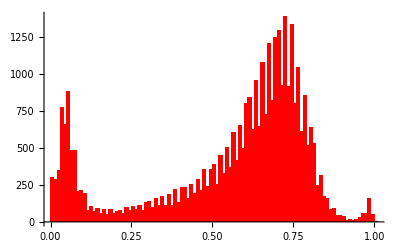

{,}

{}

riverb2.jpg

```mathematica
{RH1 = Import["river1.jpg"]}
{RH2 = ColorConvert[RH1,"Grayscale"]}
{RH3 = ColorNegate[RH2]}
HP = Histogram[Flatten[ImageData[RH3]],100,ChartStyle->Red]
{Slider[Dynamic[Trep]],Dynamic[Trep]}
Dynamic[Show[HP,ListPlot[{{Trep,0}},PlotStyle->PointSize[0.06]]]]
{RH4 = Dynamic[Binarize[RH3,Trep]]}
Export["riverb2.jpg",RH4]
```

{-Graphics-}

{-Graphics-}

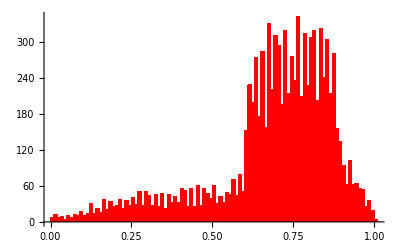

{,}

{}

```mathematica
{HL1 = Import["Heavy_load_noisy.jpg"]}
{HL2 = ColorConvert[HL1,"Grayscale"]}
HPHL = Histogram[Flatten[ImageData[HL2]],100,ChartStyle->Red]
{Slider[Dynamic[Trep]],Dynamic[Trep]}
Dynamic[Show[HPHL,ListPlot[{{Trep,0}},PlotStyle->PointSize[0.06]]]]
{HL4 = Dynamic[Binarize[HL2,Trep]]}
```

{-Graphics-}

{-Graphics-}

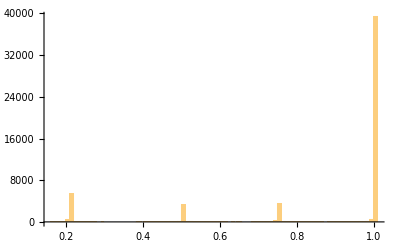

{-Graphics-}

```mathematica
{T8 = Import["problem8.jpg"]}
{T9 = ColorConvert[T8,"Grayscale"]}
HP8 = Histogram[Flatten[ImageData[T9]],100]
{T91 = ColorNegate[Binarize[T9,{0.1,0.3}]]}
```

```mathematica
{T91 = ColorNegate[Binarize[T9,{0.4,0.6}]]}
```

{-Graphics-}

```mathematica
{T91 = ColorNegate[Binarize[T9,{0.7,0.8}]]}
```

{-Graphics-}

```mathematica
{T9= ImageMultiply[T4,0.5]}
```

{-Graphics-}

```mathematica
{T10=ImageMultiply[T4,1.5]}
```

{-Graphics-}

```mathematica
{Mona = Import["mona_large.jpg"]}
MonaS = ColorSeparate[Mona]
{MonaR = MonaS[[1]]}
{MonaG = MonaS[[2]]}
{MonaB = MonaS[[3]]}
{MonaBnew = ImageMultiply[MonaB,2]}
{MonaNew = ColorCombine[{MonaR,MonaG,MonaBnew}]}
{Mona,MonaNew}
Export["MonaBnew.bmp",MonaBnew]
```

{-Graphics-}

{-Graphics-,-Graphics-,-Graphics-}

{-Graphics-}

{-Graphics-}

{-Graphics-}

«2 more identical outputs»

{-Graphics-,-Graphics-}

MonaBnew.bmp

```mathematica
f[x_]:=x^2
{Mona1 = Import["mona_large.jpg"]}
{MonaNew1 = ImageApply[f,Mona1]}
{Mona1,MonaNew1}
Export["Monaf.jpg",MonaMew1]
```

{-Graphics-}

{-Graphics-}

{-Graphics-,-Graphics-}

Monaf.jpg

```mathematica
{MonaEQ = HistogramTransform[Mona]}
{MonaRE,MonaGE,MonaBE}=ColorSeparate[MonaEQ]
ColorSeparate[MonaEQ]
{MonaR,MonaG,MonaB} = ColorSeparate[Mona]
```

{-Graphics-}

{-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-}

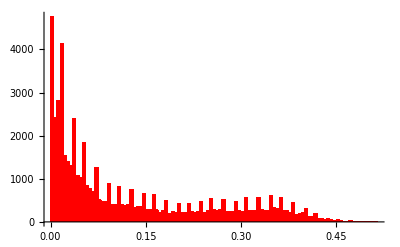

```mathematica
DataBlue = ImageData[MonaB];
DataBlueEq = ImageData[MonaBE];
HBlue = Histogram[Flatten[DataBlue],100,ChartStyle->Red]
```

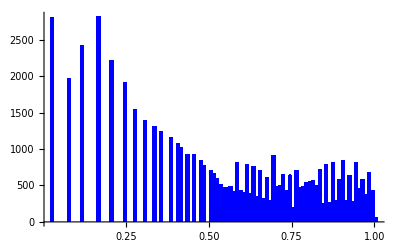

```mathematica
HBlueE = Histogram[Flatten[DataBlueEq],100,ChartStyle->Blue]
```

```mathematica
{MonaSS = Import["mona_large.jpg"]}
{MonaSSR,MonaSSG,MonaSSB} = ColorSeparate[MonaSS]
```

{-Graphics-}

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{MonaSSG=HistogramTransform[MonaG]}
```

{-Graphics-}

```mathematica
ff[x_] = Sin[10x]
{MonaSSBa = ImageApply[ff,MonaSSB]}
```

Sin[10 x]

{-Graphics-}

```mathematica
{MonaASDF = ColorCombine[{MonaSSR,MonaSSG,MonaSSBa}]}
```

{-Graphics-}

```mathematica
{P1=Import["pill1.jpg"],P2 = Import["pill2.jpg"]}
```

{-Graphics-,-Graphics-}

```mathematica
{PG1 = ColorConvert[P1,"Graylevel"],PG2 = ColorConvert[P2,"Graylevel"]}
```

{-Graphics-,-Graphics-}

```mathematica
DP1P2 = ImageDifference[PG1,PG2]
```

-Graphics-

```mathematica
ND = ColorNegate[DP1P2]
```

-Graphics-

```mathematica
I1 = Import["colorful.jpg"];
```

```mathematica
Magnify[I1,0.5]
```

-Graphics-

```mathematica
ImageDimensions[I1]
```

{251,247}

```mathematica
248/4
```

62

```mathematica
Magnify[II1=ImageCrop[I1,{248,248}],0.5]
```

-Graphics-

```mathematica
ImageDimensions[II1]
```

{248,248}

```mathematica
ImageCrop[II1,{100,100}]
```

-Graphics-

```mathematica
Magnify[ImagePartition[II1,32]//Grid,0.5]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Magnify[ImagePartition[II1,{248/2,248}],0.5]
```

{{-Graphics-,-Graphics-}}

```mathematica
Magnify[ImagePartition[II1,{248,248/2}],0.5]
```

{{-Graphics-},{-Graphics-}}

```mathematica
Magnify[II1,0.5]
```

-Graphics-

```mathematica
Magnify[S = ImagePartition[II1,{248/4,248/4}],0.5]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
S[[1]][[1]]
```

-Graphics-

```mathematica
S[[2]][[1]]
```

-Graphics-

```mathematica
ImageAssemble[{S[[1]][[1]],S[[2]][[1]]}]
```

-Graphics-

```mathematica
ImageAssemble[{S[[1]][[1]],S[[3]][[4]]}]
```

-Graphics-

```mathematica
Pirat = Import["pirat.gif"]
```

-Graphics-

```mathematica
ImageDimensions[Pirat]
```

{300,180}

```mathematica
Magnify[Pirats =ImagePartition[Pirat,{300/2,180}],0.5]
```

{{-Graphics-,-Graphics-}}

```mathematica
Pirats[[1]][[1]]
```

-Graphics-

```mathematica
Pirats[[1]][[2]]
```

-Graphics-

```mathematica
PiratsL = ColorConvert[Pirats[[1]][[1]],"Grayscale"]
```

-Graphics-

```mathematica
PiratsR = ColorConvert[Pirats[[1]][[2]],"Grayscale"]
```

-Graphics-

```mathematica
PLPR = ImageDifference[PiratsL,PiratsR]
```

-Graphics-

```mathematica
PLPR2 = ColorNegate[PLPR]
```

-Graphics-

```mathematica
Pirats
```

{{-Graphics-,-Graphics-}}

```mathematica
{Bu = Import["Bush.jpg"]}
```

{-Graphics-}

```mathematica
{Ar=Import["Arnold.jpg"]}
```

{-Graphics-}

```mathematica
Morph[t_]:=ImageAdd[ImageMultiply[Bu,1-t],ImageMultiply[Ar,t]]
{Slider[Dynamic[s]],Dynamic[s]}
```

{,}

```mathematica
{Dynamic[Morph[s]]}
```

{}